```mathematica
mu0=4*Pi*10^-7;
muB=9.27401008*10^-24;
h=6.62607*10^-34;
hbar=h/2/Pi;
```

```mathematica
Veff[s_,σx_,σz_]:=-1/(4*Sqrt[Pi]*σx^2*σz)*mu0*(9.93*muB)^2/(4*Pi)/h*10^27*N[Integrate[1/r*Integrate[(1-3*m^2)*E^(-r^2*(1-m^2)/4/σx^2)*Exp[-(m*r-s)^2/4/σz^2],{m,-1,1}],{r,1,150}]]
Vide[s_]:=mu0*(9.93*muB)^2/(4*Pi)*(2/s^3)/h*10^27
```

```mathematica
Veff[50,15,10]
```

12943.5

{{10,2925.58},{13,4683.33},{16,6628.14},{19,8615.73},{22,10509.},{25,12190.1},{28,13569.},{31,14588.1},{34,15223.2},{37,15480.},{40,15389.4},{43,14999.9},{46,14370.6},{49,13564.3},{52,12641.5},{55,11656.7},{58,10655.5},{61,9673.8},{64,8737.48},{67,7863.66},{70,7061.92},{73,6335.95},{76,5685.08},{79,5105.72},{82,4592.47},{85,4139.04},{88,3738.89},{91,3385.6},{94,3073.2},{97,2796.23},{100,2549.8},{12,4069.56}}

{{10,2.55981×10^6},{13,1.16514×10^6},{16,624953.},{19,373204.},{22,240403.},{25,163828.},{28,116609.},{31,85925.6},{34,65128.5},{37,50536.2},{40,39997.},{43,32196.},{46,26298.7},{49,21758.},{52,18205.3},{55,15385.8},{58,13119.7},{61,11277.6},{64,9764.9},{67,8511.05},{70,7463.},{73,6580.2},{76,5831.32},{79,5191.9},{82,4642.65},{85,4168.22},{88,3756.29},{91,3396.91},{94,3081.94},{97,2804.74},{100,2559.81},{12,1.48137×10^6}}

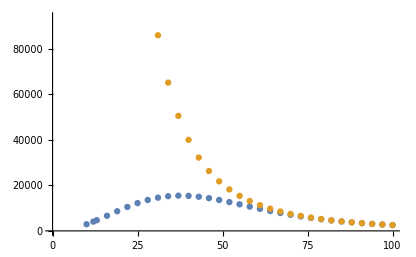

```mathematica
slist=Table[10+3n,{n,0,30}];
Vefflist=Table[{slist[[i]],Veff[slist[[i]],15,15]},{i,1,Length[slist]}]
Videlist = Table[{slist[[i]],Vide[slist[[i]]]},{i,1,Length[slist]}]
```

```mathematica
slist=Table[10+3n,{n,0,25}];
Vefflist=Table[0,{Length[slist]}];
For[i=1,i<=Length[slist],Vefflist[[i]]=Veff[slist[[i]],21,15];i++,Print["Current element:",slist[[i]]]]
Vefflist
```

Current element:10

Current element:13

Current element:16

Current element:19

Current element:22

Current element:25

Current element:28

PolynomialGCD::lrgexp: Exponent is out of bounds for function PolynomialGCD.

General::stop: Further output of PolynomialGCD::lrgexp will be suppressed during this calculation.

Current element:31

Current element:34

Current element:37

Current element:40

Current element:43

Current element:46

Current element:49

Current element:52

Current element:55

Current element:58

Current element:61

Current element:64

Current element:67

Current element:70

Current element:73

Current element:76

Current element:79

Current element:82

Current element:85

{-2948.64,-1650.74,-189.87,1339.05,2844.25,4244.66,5475.58,6491.94,7269.21,7802.13,8101.78,8191.62,8103.25,7872.22,7534.49,7123.68,6669.31,6195.75,5722.,5261.95,4824.98,4416.75,4040.04,3695.49,3382.25,3098.58}

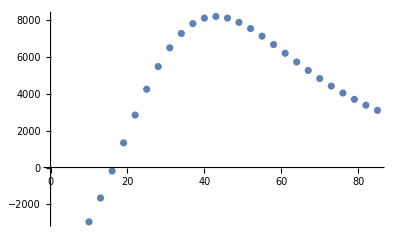

```mathematica
ListPlot[Table[{slist[[i]],Vefflist[[i]]},{i,1,Length[slist]}]]
```

Current element:10

Current element:11

Current element:12

Current element:13

Current element:14

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {2.28925}. NIntegrate obtained -0.242182 and 0.055705 for the integral and error estimates.

Current element:15

Current element:16

Current element:17

Current element:18

Current element:19

Current element:20

Current element:21

Current element:22

Current element:23

Current element:24

Current element:25

{12943.5,13339.8,13584.8,13646.2,13879.5,13266.8,12898.7,12466.6,12005.3,11541.3,11092.9,10671.5,10283.3,9930.77,9613.76,9330.55}

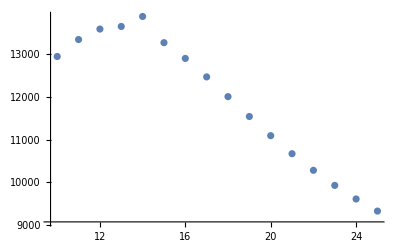

```mathematica
zlist=Table[10+n,{n,0,15}];
Vefflist=Table[0,{Length[zlist]}];
For[i=1,i<=Length[zlist],Vefflist[[i]]=Veff[50,15,zlist[[i]]];i++,Print["Current element:",zlist[[i]]]]
Vefflist
ListPlot[Table[{zlist[[i]],Vefflist[[i]]},{i,1,Length[zlist]}]]
```

Current element:8

Current element:9

Current element:10

Current element:11

Current element:12

Current element:13

Current element:14

Current element:15

Current element:16

Current element:17

Current element:18

Current element:19

Current element:20

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {2.20031}. NIntegrate obtained -0.290683 and 0.000173317 for the integral and error estimates.

Current element:21

Current element:22

Current element:23

Current element:24

Current element:25

Current element:26

{7845.89,8041.29,8218.5,8333.02,8349.31,8253.51,8053.21,7769.77,7429.81,7059.,6678.8,6305.38,5949.68,5619.02,5316.39,5043.13,4798.76,4581.8,4390.15}

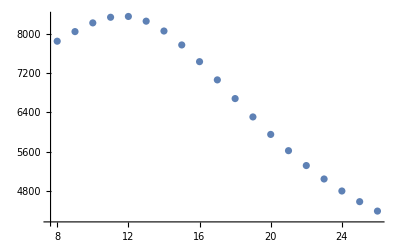

```mathematica
zlist=Table[8+n,{n,0,18}];
Vefflist=Table[0,{Length[zlist]}];
For[i=1,i<=Length[zlist],Vefflist[[i]]=Veff[50,21,zlist[[i]]];i++,Print["Current element:",zlist[[i]]]]
Vefflist
ListPlot[Table[{zlist[[i]],Vefflist[[i]]},{i,1,Length[zlist]}]]
```